```mathematica
earr = <||>
esc[k_,n_]:=(*Probability that exactly k leave the first n*)
If[k>n||k<0,0.,
If[n==0, 1.,
Lookup[earr,Key[{k,n}],
Module[{out=2^(-n)esc[k-1,n-1]+(1-2^(-n))esc[k,n-1]},
AppendTo[earr,{k,n}->out];out]]
]]
```

<||>

```mathematica
esc[0,10]
```

0.28907

```mathematica
esc[1,11]
```

0.350357

```mathematica
esc[0,11]
```

0.577717

```mathematica
esc[0,0]
esc[1,0]
```

1.

0.

```mathematica
earr
```

<|{1,1}→1/4|>

```mathematica
esclt[eps_,n_]:=Sum[esc[k,n],{k,0,Floor[eps n]}]
escltk[k_,n_]:=Sum[esc[i,n],{i,0,k}]
```

```mathematica
DiscretePlot[Sum[1-esclt[.1,k],{k,0,n}],{n,0,500},PlotRange->{0,1}]
```

$Aborted

```mathematica
Product[esclt[.1,k],{k,10,100}]
```

0.0383111

```mathematica
esclt[0.1,100]
```

1.

```mathematica
Monitor[esclt[0.1,40],earr]
```

0.999997

```mathematica
Lookup[earr,Key[{3,40}]]
```

Missing[KeyAbsent,{3,40}]

```mathematica
earr
```

<||>

```mathematica
iterate[l_]:=Module[{n=Length[l]},(1-2^(-n))Append[l,0]+2^(-n)Prepend[l,0]]
```

```mathematica
iterate@iterate@iterate@{1}//N
```

{0.328125,0.484375,0.171875,0.015625}

```mathematica
Table[esc[k,3],{k,0,3}]
```

{0.328125,0.484375,0.171875,0.015625}

```mathematica
iterates = {{1.}}
```

{{1.}}

```mathematica
getiter[n_]:=(While[Length[iterates]<=n, AppendTo[iterates,iterate[Last[iterates]]]];iterates[[n+1]])
```

```mathematica
getiter[0]
```

{1.}

```mathematica
getiter[1]
```

{0.5,0.5}

```mathematica
getiter[2]
```

{0.375,0.5,0.125}

```mathematica
getiter[100]
```

{0.288788,0.463994,0.208524,0.0359126,0.00268651,0.0000929195,1.5373×10^-6,1.24012×10^-8,4.93133×10^-11,9.72675×10^-14,9.55015×10^-17,4.67687×10^-20,1.14363×10^-23,1.39723×10^-27,8.5319×10^-32,2.60437×10^-36,3.97446×10^-41,3.03248×10^-46,1.15684×10^-51,2.20654×10^-57,2.10434×10^-63,1.00343×10^-69,2.39238×10^-76,2.85195×10^-83,1.69989×10^-90,5.06608×10^-98,7.54905×10^-106,5.62448×10^-114,2.09528×10^-122,3.90277×10^-131,3.63473×10^-140,1.69256×10^-149,3.94079×10^-159,4.58768×10^-169,2.67038×10^-179,7.77183×10^-190,1.13095×10^-200,8.22875×10^-212,2.9936×10^-223,5.44533×10^-235,4.9525×10^-247,2.25214×10^-259,5.12076×10^-272,5.82163×10^-285,3.30922×10^-298,9.40536×10^-312,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

```mathematica
Animate[ListPlot[getiter[n], PlotRange -> {0,1}],{n,0,100,1}]
```

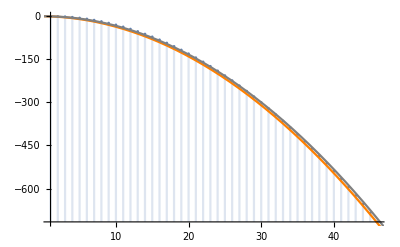

```mathematica
Show[
DiscretePlot[Log[getiter[300][[x]]],{x,0,100},PlotRange->All],
Plot[-x(x+1)/3,{x,0,60}, PlotStyle->Orange,PlotRange->All],
Plot[-x^2/3,{x,0,60}, PlotStyle->Gray,PlotRange->All]
]
```

```mathematica
Exp[3]//N
```

20.0855

```mathematica
Product[(1-2^(-n)),{n,1,∞}]
```

QPochhammer[1/2,1/2]

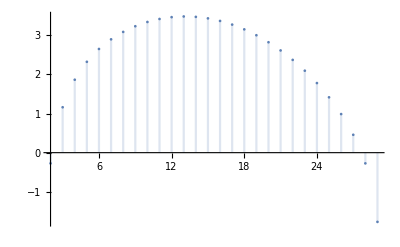

```mathematica
DiscretePlot[Log[getiter[300][[x]]-Exp[-x^2/3]]+x^2/3,{x,0,100},PlotRange->All]
```

```mathematica
lses[x_,y_]:=Log[1+Exp[y-x]]+x (*x should be the largest number*)
lse[x_,y_]:=lses[Max[x,y],Min[x,y]]
```

```mathematica
literates = {{0.}}
literate[l_]:=Module[{n=Length[l]},MapThread[lse,{Log[1-2^(-n)]+Append[l,-∞],-n Log[2]+Prepend[l,-∞]}]]
getliter[n_]:=(While[Length[literates]<=n, AppendTo[literates,literate[Last[literates]]]];literates[[n+1]])
```

{{0.}}

```mathematica
getliter[1000]
```

{-1.24206,-0.767883,-1.5677,-3.32667,-5.91951,-9.28378,-13.3855,-18.2055,-23.7328,-29.9613,-36.8874,-44.5091,-52.8252,-61.8353,-71.5389,-81.9359,-93.0261,-104.81,-117.286,-130.456,-144.319,-158.875,-174.124,-190.067,-206.702,-224.031,-242.053,-260.768,-280.176,-300.277,-321.071,-342.559,-364.74,-387.614,-411.181,-435.441,-460.394,-486.04,-512.38,-539.413,-567.139,-595.558,-624.67,-654.475,-684.974,-716.165,-748.05,-780.628,-813.899,-847.863,-882.521,-917.871,-953.915,-990.652,-1028.08,-1066.2,-1105.02,-1144.53,-1184.73,-1225.63,-1267.22,-1309.5,-1352.47,-1396.14,-1440.5,-1485.56,-1531.31,-1577.75,-1624.88,-1672.71,-1721.23,-1770.44,-1820.35,-1870.95,-1922.24,-1974.23,-2026.91,-2080.28,-2134.34,-2189.1,-2244.55,-2300.7,-2357.54,-2415.07,-2473.29,-2532.21,-2591.82,-2652.13,-2713.12,-2774.81,-2837.2,-2900.27,-2964.04,-3028.5,-3093.66,-3159.51,-3226.05,-3293.29,-3361.21,-3429.84,-3499.15,-3569.16,-3639.86,-3711.25,-3783.34,-3856.12,-3929.6,-4003.76,-4078.62,-4154.18,-4230.42,-4307.36,-4384.99,-4463.32,-4542.34,-4622.05,-4702.45,-4783.55,-4865.34,-4947.83,-5031.01,-5114.88,-5199.44,-5284.7,-5370.65,-5457.29,-5544.63,-5632.66,-5721.38,-5810.8,-5900.91,-5991.71,-6083.2,-6175.39,-6268.27,-6361.85,-6456.12,-6551.08,-6646.73,-6743.08,-6840.12,-6937.85,-7036.28,-7135.4,-7235.21,-7335.72,-7436.92,-7538.81,-7641.4,-7744.68,-7848.65,-7953.31,-8058.67,-8164.72,-8271.47,-8378.91,-8487.04,-8595.86,-8705.38,-8815.59,-8926.49,-9038.09,-9150.38,-9263.36,-9377.04,-9491.41,-9606.47,-9722.23,-9838.68,-9955.82,-10073.7,-10192.2,-10311.4,-10431.3,-10551.9,-10673.2,-10795.2,-10917.9,-11041.3,-11165.4,-11290.1,-11415.6,-11541.7,-11668.6,-11796.1,-11924.4,-12053.3,-12182.9,-12313.2,-12444.2,-12575.9,-12708.3,-12841.4,-12975.2,-13109.6,-13244.8,-13380.7,-13517.2,-13654.5,-13792.4,-13931.,-14070.3,-14210.4,-14351.1,-14492.5,-14634.6,-14777.3,-14920.8,-15065.,-15209.9,-15355.4,-15501.7,-15648.6,-15796.3,-15944.6,-16093.6,-16243.4,-16393.8,-16544.9,-16696.7,-16849.2,-17002.4,-17156.2,-17310.8,-17466.1,-17622.,-17778.7,-17936.,-18094.1,-18252.8,-18412.2,-18572.3,-18733.1,-18894.6,-19056.8,-19219.7,-19383.3,-19547.6,-19712.6,-19878.2,-20044.6,-20211.6,-20379.4,-20547.8,-20716.9,-20886.7,-21057.3,-21228.5,-21400.4,-21573.,-21746.3,-21920.2,-22094.9,-22270.3,-22446.3,-22623.1,-22800.5,-22978.7,-23157.5,-23337.,-23517.2,-23698.2,-23879.8,-24062.1,-24245.,-24428.7,-24613.1,-24798.2,-24983.9,-25170.4,-25357.5,-25545.4,-25733.9,-25923.2,-26113.1,-26303.7,-26495.,-26687.,-26879.7,-27073.1,-27267.2,-27461.9,-27657.4,-27853.6,-28050.4,-28248.,-28446.2,-28645.1,-28844.8,-29045.1,-29246.1,-29447.8,-29650.2,-29853.3,-30057.1,-30261.6,-30466.7,-30672.6,-30879.2,-31086.4,-31294.4,-31503.,-31712.3,-31922.3,-32133.1,-32344.5,-32556.6,-32769.4,-32982.9,-33197.,-33411.9,-33627.5,-33843.7,-34060.7,-34278.4,-34496.7,-34715.7,-34935.5,-35155.9,-35377.,-35598.8,-35821.3,-36044.5,-36268.4,-36493.,-36718.2,-36944.2,-37170.9,-37398.2,-37626.3,-37855.,-38084.4,-38314.5,-38545.4,-38776.9,-39009.1,-39242.,-39475.6,-39709.9,-39944.8,-40180.5,-40416.9,-40653.9,-40891.7,-41130.1,-41369.2,-41609.1,-41849.6,-42090.8,-42332.7,-42575.3,-42818.6,-43062.6,-43307.3,-43552.7,-43798.7,-44045.5,-44292.9,-44541.1,-44789.9,-45039.5,-45289.7,-45540.6,-45792.2,-46044.5,-46297.5,-46551.2,-46805.6,-47060.7,-47316.5,-47572.9,-47830.1,-48087.9,-48346.5,-48605.7,-48865.6,-49126.3,-49387.6,-49649.6,-49912.3,-50175.7,-50439.8,-50704.6,-50970.,-51236.2,-51503.1,-51770.6,-52038.9,-52307.8,-52577.4,-52847.8,-53118.8,-53390.5,-53662.9,-53936.,-54209.8,-54484.3,-54759.5,-55035.3,-55311.9,-55589.2,-55867.1,-56145.8,-56425.1,-56705.1,-56985.9,-57267.3,-57549.4,-57832.2,-58115.7,-58399.9,-58684.8,-58970.3,-59256.6,-59543.6,-59831.2,-60119.6,-60408.6,-60698.3,-60988.8,-61279.9,-61571.7,-61864.2,-62157.4,-62451.3,-62745.9,-63041.2,-63337.2,-63633.8,-63931.2,-64229.2,-64528.,-64827.4,-65127.6,-65428.4,-65729.9,-66032.1,-66335.,-66638.6,-66942.9,-67247.9,-67553.6,-67859.9,-68167.,-68474.8,-68783.2,-69092.4,-69402.2,-69712.7,-70024.,-70335.9,-70648.5,-70961.8,-71275.8,-71590.5,-71905.8,-72221.9,-72538.7,-72856.2,-73174.3,-73493.2,-73812.7,-74132.9,-74453.9,-74775.5,-75097.8,-75420.8,-75744.5,-76068.9,-76394.,-76719.8,-77046.2,-77373.4,-77701.3,-78029.8,-78359.,-78689.,-79019.6,-79350.9,-79683.,-80015.7,-80349.1,-80683.2,-81018.,-81353.4,-81689.6,-82026.5,-82364.1,-82702.3,-83041.3,-83380.9,-83721.2,-84062.3,-84404.,-84746.4,-85089.5,-85433.3,-85777.8,-86123.,-86468.9,-86815.4,-87162.7,-87510.7,-87859.3,-88208.7,-88558.7,-88909.4,-89260.9,-89613.,-89965.8,-90319.3,-90673.5,-91028.4,-91384.,-91740.3,-92097.2,-92454.9,-92813.2,-93172.3,-93532.,-93892.5,-94253.6,-94615.4,-94977.9,-95341.2,-95705.1,-96069.7,-96434.9,-96800.9,-97167.6,-97535.,-97903.,-98271.8,-98641.2,-99011.4,-99382.2,-99753.7,-100126.,-100499.,-100872.,-101247.,-101622.,-101997.,-102374.,-102751.,-103129.,-103507.,-103886.,-104266.,-104647.,-105028.,-105410.,-105792.,-106176.,-106560.,-106944.,-107330.,-107716.,-108103.,-108490.,-108878.,-109267.,-109657.,-110047.,-110438.,-110830.,-111222.,-111615.,-112009.,-112403.,-112798.,-113194.,-113590.,-113988.,-114385.,-114784.,-115183.,-115583.,-115984.,-116385.,-116787.,-117190.,-117593.,-117997.,-118402.,-118808.,-119214.,-119621.,-120028.,-120437.,-120846.,-121255.,-121665.,-122077.,-122488.,-122901.,-123314.,-123728.,-124142.,-124557.,-124973.,-125390.,-125807.,-126225.,-126644.,-127063.,-127483.,-127904.,-128325.,-128747.,-129170.,-129594.,-130018.,-130443.,-130868.,-131295.,-131722.,-132149.,-132578.,-133007.,-133437.,-133867.,-134298.,-134730.,-135162.,-135596.,-136030.,-136464.,-136899.,-137335.,-137772.,-138210.,-138648.,-139086.,-139526.,-139966.,-140407.,-140848.,-141291.,-141733.,-142177.,-142621.,-143066.,-143512.,-143958.,-144406.,-144853.,-145302.,-145751.,-146201.,-146651.,-147103.,-147555.,-148007.,-148460.,-148914.,-149369.,-149825.,-150281.,-150737.,-151195.,-151653.,-152112.,-152572.,-153032.,-153493.,-153954.,-154417.,-154880.,-155343.,-155808.,-156273.,-156739.,-157205.,-157672.,-158140.,-158609.,-159078.,-159548.,-160019.,-160490.,-160962.,-161435.,-161908.,-162382.,-162857.,-163333.,-163809.,-164286.,-164763.,-165242.,-165721.,-166200.,-166681.,-167162.,-167643.,-168126.,-168609.,-169093.,-169577.,-170062.,-170548.,-171035.,-171522.,-172010.,-172499.,-172988.,-173478.,-173969.,-174460.,-174953.,-175445.,-175939.,-176433.,-176928.,-177424.,-177920.,-178417.,-178915.,-179413.,-179912.,-180412.,-180912.,-181413.,-181915.,-182418.,-182921.,-183425.,-183930.,-184435.,-184941.,-185448.,-185955.,-186463.,-186972.,-187481.,-187991.,-188502.,-189014.,-189526.,-190039.,-190553.,-191067.,-191582.,-192098.,-192614.,-193131.,-193649.,-194167.,-194686.,-195206.,-195727.,-196248.,-196770.,-197293.,-197816.,-198340.,-198865.,-199390.,-199916.,-200443.,-200971.,-201499.,-202028.,-202557.,-203087.,-203618.,-204150.,-204682.,-205215.,-205749.,-206284.,-206819.,-207354.,-207891.,-208428.,-208966.,-209505.,-210044.,-210584.,-211124.,-211666.,-212208.,-212751.,-213294.,-213838.,-214383.,-214928.,-215475.,-216022.,-216569.,-217117.,-217666.,-218216.,-218766.,-219317.,-219869.,-220422.,-220975.,-221529.,-222083.,-222638.,-223194.,-223751.,-224308.,-224866.,-225425.,-225984.,-226544.,-227105.,-227666.,-228229.,-228791.,-229355.,-229919.,-230484.,-231050.,-231616.,-232183.,-232751.,-233319.,-233888.,-234458.,-235028.,-235599.,-236171.,-236744.,-237317.,-237891.,-238466.,-239041.,-239617.,-240194.,-240771.,-241349.,-241928.,-242507.,-243088.,-243668.,-244250.,-244832.,-245415.,-245999.,-246583.,-247168.,-247754.,-248340.,-248927.,-249515.,-250104.,-250693.,-251283.,-251873.,-252464.,-253056.,-253649.,-254242.,-254836.,-255431.,-256027.,-256623.,-257219.,-257817.,-258415.,-259014.,-259614.,-260214.,-260815.,-261416.,-262019.,-262622.,-263226.,-263830.,-264435.,-265041.,-265647.,-266255.,-266863.,-267471.,-268080.,-268690.,-269301.,-269912.,-270524.,-271137.,-271751.,-272365.,-272980.,-273595.,-274211.,-274828.,-275446.,-276064.,-276683.,-277303.,-277923.,-278544.,-279166.,-279788.,-280411.,-281035.,-281660.,-282285.,-282911.,-283538.,-284165.,-284793.,-285422.,-286051.,-286681.,-287312.,-287943.,-288575.,-289208.,-289842.,-290476.,-291111.,-291746.,-292383.,-293020.,-293657.,-294296.,-294935.,-295575.,-296215.,-296856.,-297498.,-298141.,-298784.,-299428.,-300073.,-300718.,-301364.,-302011.,-302658.,-303306.,-303955.,-304604.,-305255.,-305905.,-306557.,-307209.,-307862.,-308516.,-309170.,-309825.,-310481.,-311137.,-311794.,-312452.,-313111.,-313770.,-314430.,-315090.,-315752.,-316414.,-317076.,-317740.,-318404.,-319068.,-319734.,-320400.,-321067.,-321734.,-322402.,-323071.,-323741.,-324411.,-325082.,-325754.,-326426.,-327099.,-327773.,-328447.,-329122.,-329798.,-330475.,-331152.,-331830.,-332508.,-333188.,-333868.,-334548.,-335230.,-335912.,-336594.,-337278.,-337962.,-338647.,-339332.,-340019.,-340706.,-341393.,-342081.,-342770.,-343460.,-344151.,-344842.,-345534.,-346226.,-346920.}

```mathematica
getiter[100]//Log
```

{-1.24206,-0.767883,-1.5677,-3.32667,-5.91951,-9.28378,-13.3855,-18.2055,-23.7328,-29.9613,-36.8874,-44.5091,-52.8252,-61.8353,-71.5389,-81.9359,-93.0261,-104.81,-117.286,-130.456,-144.319,-158.875,-174.124,-190.067,-206.702,-224.031,-242.053,-260.768,-280.176,-300.277,-321.071,-342.559,-364.74,-387.614,-411.181,-435.441,-460.394,-486.04,-512.38,-539.413,-567.139,-595.558,-624.67,-654.475,-684.974,-716.165,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}

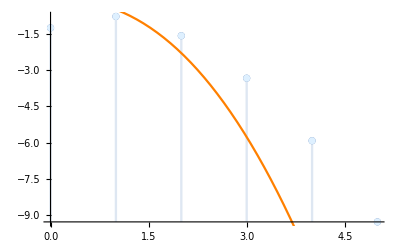

```mathematica
Show[DiscretePlot[getliter[100][[x+1]],{x,0,5},PlotRange->All],
DiscretePlot[getliter[1000][[x+1]],{x,0,5},PlotRange->All,PlotStyle->LightBlue],
Plot[-Log[x+1]x(x+1)Log[2]/2,{x,0,5},PlotRange->All,PlotStyle->Orange]]
```

```mathematica
lbounds = {0.}
lbiterate[last_,k_]:=lse[-k(k+1)Log[2]/2,-k Log[2]+last];
getlbound[n_]:=(While[Length[lbounds]<=n+1, AppendTo[lbounds,lbiterate[Last[lbounds],Length[lbounds]]]];lbounds[[n+1]])
```

{0.}

```mathematica
getlbound[1]
```

0.

```mathematica
getliter[1][[2]]/Log[2]
```

-1.

```mathematica
getliter[2][[3]]/Log[2]
```

-3.

```mathematica
getliter[3][[4]]/Log[2]
```

-6.

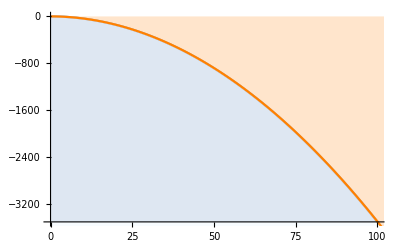

```mathematica
Show[DiscretePlot[getliter[100][[x+1]],{x,0,5000},PlotRange->All],
DiscretePlot[getliter[1000][[x+1]],{x,0,5000},PlotRange->All,PlotStyle->LightBlue],
DiscretePlot[getlbound[x],{x,0,5000},PlotRange->All,PlotStyle->Orange]]
```

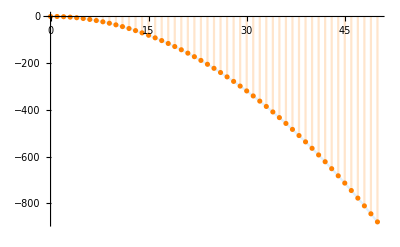

```mathematica
Show[Plot[Log[x+1]-Log[2]x(x+1)/2,{x,0,50},PlotRange->All,PlotStyle->LightBlue],
DiscretePlot[getlbound[x],{x,0,50},PlotRange->All,PlotStyle->Orange]]
```

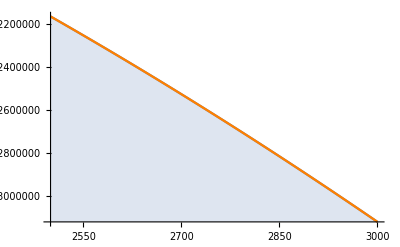

```mathematica
Show[DiscretePlot[getliter[3000][[x+1]],{x,2500,3000},PlotRange->All],
Plot[Log[x+1]-Log[2]x(x+1)/2,{x,2500,3000},PlotRange->All,PlotStyle->Orange]]
```

```mathematica
Length[literates]
```

3548

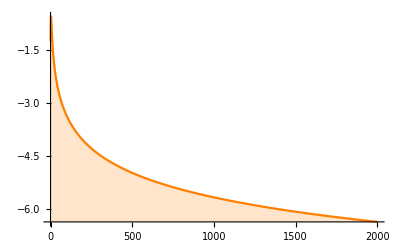

```mathematica
DiscretePlot[getliter[3000][[x+1]]-(Log[x+1]-Log[2]x(x+1)/2),{x,0,2000},PlotRange->All,PlotStyle->Orange]
```